```mathematica
FinancialData["NASDAQ:AMZN","Price"]
```

1 883.16 $

```mathematica
FinancialData["NASDAQ:AMZN","Close"]
```

1 883.16 $

```mathematica
amzn=FinancialData["NASDAQ:AMZN","Close",All]
```

TimeSeries[…]

```mathematica
data=Map[#-1&,Ratios@amzn["Values"]]
```

{-0.117407,-0.0115674,-0.042715,-0.127751,-0.0217239,0.0744985,0.056,-0.0328283,-0.0169712,-0.00398409,0.00733336,-0.0211781,-0.0419202,0.0882145,0.0745784,0.0187085,-0.0616114,-0.0267235,0.0404302,-0.0124688,-0.00694447,-0.0425937,0.00332005,0.013898,-0.0039164,-0.017038,0.00733336,-1.11022×10^-16,-1.11022×10^-16,-0.0138981,0.0348994,-0.0168612,0.048153,0.203272,0.0460251,0.151,0.00912246,0.103315,-0.105735,-0.0680629,-0.000276146,0.0929986,-0.0492716,-0.0279405,0.0120538,-0.0215301,0.0730338,-0.0135254,-0.014153,0.0421713,0.0671546,-0.0125051,-0.0212418,0.00876467,-0.0430286,-0.0449632,0.0185604,-0.0324444,0.052825,0.0157068,-0.055842,0.,-0.0186533,-0.0194715,-0.0346714,0.061386,0.,-0.0239963,0.00472813,0.0442353,0.0563317,-0.0110922,0.0245901,-0.0151579,0.00641304,-0.00849617,0.0934019,-0.0203762,0.2,0.07986,0.0192926,-0.0439359,0.168198,-0.161063,0.0840853,0.0157536,-0.033754,0.199271,0.139818,0.0277778,-0.0540541,-0.0678857,0.0218244,-0.0299976,0.0734786,-0.0732888,-0.00248688,0.00124648,0.0271415,-0.0162424,-0.0128142,-0.0639042,0.0402667,0.0253781,-0.00524998,-0.0143252,-0.0757267,0.,0.0546207,0.157991,0.0212333,-0.00464497,0.116889,-0.150219,0.158511,0.0895311,-0.0493415,-0.00799998,-0.00216368,-0.0224719,-0.0169389,-0.0436923,-0.0392193,-0.0603148,-0.06201,-0.0448759,0.0236473,0.0795337,0.0499161,0.00959996,0.0212815,0.0161827,-0.0205062,-0.0581291,-0.00614803,0.0137997,-0.0319174,0.0353528,-0.00838947,0.0306965,0.0309279,0.0208889,0.0250327,-0.00445953,-0.037756,0.0392374,-0.0311434,0.00924709,-0.0272688,-0.0152501,-0.000086441,-0.0225368,0.0946788,-0.0155385,-0.00454052,-0.0180278,0.0506525,0.0208421,0.0354712,-0.0123481,-0.0421456,0.0187369,-0.0117793,-0.0349227,-0.0608883,-0.00738349,0.0799628,0.0492897,0.016,-0.0325056,0.0335977,0.0242277,0.0124187,-0.0385514,-0.0253139,-0.0130896,0.00442103,0.0394048,-0.00846951,0.0571487,-0.00904193,-0.017084,-0.0246889,-0.00627787,-0.0108009,0.092295,-0.00188612,-0.00585783,-0.0138757,-0.00809566,-0.0141858,0.0307511,0.00803209,0.0258016,-0.000140573,0.0154932,0.104372,0.0583869,-0.00981763,-0.0590179,0.0235825,0.0212418,0.02336,0.0880238,-0.00477516,-0.0418393,-0.0141652,0.00244578,0.00386247,0.0111904,0.0680487,-0.0154712,0.,-0.00214284,0.00515387,-0.0303375,0.0129259,0.0301624,0.00746058,-0.00405202,0.0537318,0.0547024,-0.0216957,-0.0469677,-0.0381803,0.0440596,0.0702441,-0.00982616,0.0304071,-0.0108656,-0.0000735702,-0.0122853,-0.00733065,-0.0124777,-0.0625322,-0.0716545,0.0478518,-0.0250247,0.155597,-0.00125483,-0.0393266,0.0299503,0.00800003,-0.016125,-0.0355954,0.00690388,0.0150316,-0.0000117072,0.,0.00546771,-0.0140827,-0.0212292,-0.0174052,0.0262978,-0.0193839,-0.00284327,-0.0268839,-0.0479977,0.058039,-0.00789579,0.0254119,-0.0283224,0.0204596,-0.0330047,0.0385336,0.00847802,0.0452882,0.108055,0.0560759,0.15475,-0.0239992,0.0778991,0.119719,0.0730177,-0.0894205,0.0538633,0.0733732,0.139023,0.0769031,-0.00751383,-0.0485737,0.0477433,0.0100857,0.14412,0.070091,0.,-0.00816542,-0.115603,-0.0151729,-0.0568721,0.0816605,0.0685435,-0.0000156234,-0.0141235,0.0567845,0.147629,-0.039534,0.0146745,-0.0475956,-0.026421,0.0105316,-0.0527593,-0.0935277,0.0550559,-0.0252712,-0.0236591,0.0150205,-0.0773877,0.0801501,0.0593589,0.0485018,0.0195353,0.0513863,-0.0220443,-0.0372235,-0.0249768,0.0751955,0.000512853,0.00288924,0.00436782,0.039047,-0.0231978,-0.03323,-0.064831,-0.110164,-0.209077,-0.0453829,0.0990958,-0.0227707,0.00436681,0.0695652,-0.084013,-0.0576782,-0.0447517,-0.0312295,-0.0093232,0.157586,-0.0888029,0.0349637,0.0728806,0.0314386,0.192067,-0.0285372,0.0697961,0.0583118,-0.0216286,-0.0132598,-0.0806278,0.0743101,-0.0385306,0.0217977,-0.137336,-0.0775899,0.0580106,0.0219833,-0.0195081,0.0233108,0.0380519,0.0244792,0.0634767,0.00947517,0.0304631,0.0425985,0.0125033,0.010773,0.,-0.0026326,0.0165189,0.062506,0.0361125,-0.0376935,0.0297178,-0.0100946,-0.0306299,0.0185444,0.038447,-0.0389362,0.0345574,-0.0247924,-0.0117415,0.176219,0.104376,-0.0655501,0.17863,0.206922,-0.0160542,0.,0.0099021,-0.113672,0.0911562,-0.0477418,-0.0501263,-0.00526544,0.0132731,0.0683861,0.0597159,-0.0144554,0.0463303,-0.00335512,0.0922466,0.190506,-0.0423882,0.0359242,0.11182,0.0113694,0.00815202,-0.000572271,0.0835119,-0.0557751,-0.0332831,0.,0.104871,0.0522846,0.108434,0.151268,0.0086546,0.152106,-0.115098,-0.0941086,-0.0675676,0.0172174,-0.00400362,-0.191783,-0.0619469,0.160377,-0.086374,0.0241867,0.0914991,-0.0218826,-0.0483251,-0.00908177,-0.0485519,0.14059,-0.0616302,-0.018,-0.0582605,-0.0836197,-0.02562,0.12764,-0.0489192,-0.0562201,-0.0519645,-0.0427807,0.138268,0.0453988,0.0815737,-0.0368928,0.126755,0.025,0.0380488,-0.0878646,0.0180193,-0.0273198,0.011438,0.00566258,0.0634236,0.0553219,-0.0164083,-0.0115811,0.0421862,-0.0368798,-0.0210292,0.0567756,-0.0243692,-0.0226855,-0.0956439,0.0361299,0.13087,-0.00580952,0.0759631,0.100662,0.0455432,-0.00689946,0.0906433,-0.0194316,-0.0386164,0.0181215,0.0216537,0.00853912,-0.0328653,-0.0585191,-0.00409442,0.136024,-0.163486,0.0821857,0.0421512,0.0603291,0.105543,-0.0139727,-0.0063324,-0.0601139,-0.130491,0.0226686,-0.12278,-0.0525912,0.0244755,-0.0622798,-0.00727929,0.076993,0.0102127,-0.0366502,-0.0485386,-0.026647,0.0396598,-0.0363303,0.0523124,-0.0626953,-0.0172,-0.0860583,-0.0505328,0.0840355,-0.0527148,0.036553,-0.108935,0.0596518,-0.0629827,0.0321138,0.0824249,-0.0495161,0.021835,0.017,-0.0873225,-0.105151,-0.0231033,0.207438,0.0111919,-0.0143796,0.109474,-0.048583,0.00212766,-0.0350234,-0.0302607,0.00454139,0.0485689,0.0780776,-0.0219778,0.0137936,0.0226657,-0.0394086,0.0215301,0.00803213,-0.064741,0.0745559,0.0703582,0.0338074,-0.013886,-0.0431459,-0.0877985,0.0442203,-0.14549,0.0688137,-0.0752942,-0.0466122,0.0470297,-0.0395839,-0.014769,-0.0606012,0.00930851,-0.0704864,0.102763,-0.0790499,-0.0453583,0.0643275,-0.00068128,0.00892912,0.0619902,0.00899451,0.111235,0.0354783,-0.0618779,0.0688993,0.0435303,0.0142597,0.0973314,-0.00948767,-0.0153257,-0.0719844,0.0429853,-0.0427253,0.00892815,0.0395421,8.00361×10^-6,-1.11022×10^-16,0.0190109,0.0451866,-0.0479248,0.0424399,-0.00662879,-0.00476644,-0.022023,-0.016658,-0.00796813,0.060241,-0.0568182,0.0441767,-0.0374923,0.0529386,0.225806,-0.0100557,-0.0336261,-0.00242718,0.0178492,0.0509957,0.0591292,0.0221904,-0.00980392,-0.038891,-0.0588665,-0.00430336,-0.0569264,-0.0133221,0.0345921,0.050571,0.00310559,-0.0263158,0.0524642,-0.0181269,-0.0653784,-0.0600885,-0.0105079,-0.0212389,-0.0388716,-0.00847412,-0.0417457,0.0287208,0.201146,-0.092141,0.0167624,0.0190972,0.0213016,-0.0191892,0.0739864,-0.030885,0.0187974,0.,0.0328722,0.015528,0.0672783,0.0673352,-0.0288537,-0.059433,-0.000740669,0.0478,-0.0280757,0.0137184,-0.019225,0.0290485,0.172894,0.0312876,-0.0431739,-0.0670732,0.00915033,-0.0168394,-0.0085639,0.0312292,0.0296392,-0.0218973,-0.0786996,-0.0986111,0.0146441,0.0144205,-0.0531377,-0.0371603,0.174056,-0.0783217,-0.153263,-0.0967742,0.106151,-0.00716766,-0.037044,-0.0487805,0.0404419,-0.0255999,-0.00194553,0.0419182,-0.0308773,-0.0164093,0.101079,-0.0124777,-0.0640722,0.0327866,-0.0728361,0.041289,0.0435281,0.122327,0.112311,-0.0668147,-0.0453522,0.108333,-0.0406015,-0.0446645,0.,-0.0229695,-0.00839625,-0.0423367,-0.0238796,-0.0615942,-0.0183321,0.0580054,0.0176655,0.0100382,-0.0488246,0.0475285,-0.0435572,-0.050277,-0.00100698,0.023008,-0.00685038,0.0019685,0.0815403,-0.0281633,-0.0233645,-0.0160291,-0.00802299,0.0392157,-0.0207547,-0.0105895,0.134363,-0.0291776,-0.04244,0.0710908,0.00862069,-0.0410256,-0.0552585,0.00377358,0.0075188,-0.0512985,0.00589966,-0.0273703,0.0331575,0.0515643,-0.067537,0.00595238,-0.110454,-0.125277,-0.0608365,0.0526316,0.126933,-0.0273035,-0.0198922,-0.0417661,0.0448418,-9.52983×10^-6,0.00834327,0.0437447,0.0860694,-0.0636157,-0.0356347,0.0173302,0.0590142,-0.0393895,0.00418458,-0.0711111,0.0502392,-0.0205011,0.0430326,0.0535112,0.0327955,-0.0922131,-0.0496614,-0.0142518,-0.0963855,0.0360107,-0.0579248,0.0163934,0.112903,-0.0664155,0.0388094,0.153164,-0.0583153,-0.0665138,0.0184373,0.00119662,0.00603373,-0.0718556,0.0116025,-0.0522857,-0.00269176,-0.00675836,-0.0149348,0.0179198,-0.00134418,-0.0882053,-0.193452,0.00185977,0.0754906,0.0376712,-0.019802,-0.0218721,0.0189189,-0.0135135,-0.0119726,0.00171922,-0.0293979,-0.00714428,0.00719568,-0.00179676,0.214286,-0.0323529,0.0273556,-0.0295858,-0.0167561,0.0201424,-0.0577508,-0.0290323,-0.089701,-0.0839416,-0.0438247,0.00416667,0.00414938,0.0186116,0.0222958,0.031746,0.0404,-0.0258776,-0.0626328,-0.0141539,0.106774,0.0352351,0.0770753,0.0282725,-0.00970874,0.0196078,-0.0384615,-0.0266667,0.0633699,0.0144797,0.0142984,-0.0203565,0.0127796,0.0836088,-0.0334901,0.,0.100916,0.00409298,-0.0517711,-0.0129195,-0.0131119,0.00738642,-0.00586815,0.0574374,-0.0278552,-0.0186132,-0.0481863,-0.0797546,0.0683467,0.0343085,-0.025641,-0.0154799,-0.0471698,0.0165017,-0.0016104,-0.0666788,-0.0226342,0.0267233,-0.0676945,-0.0595894,-0.047524,0.0124738,-0.0862573,-0.0966292,0.131841,-0.145055,-0.0976658,0.145273,0.104478,0.11036,-0.0263692,-0.0145833,0.0782241,0.156863,-0.0338983,-0.077193,0.114068,0.0204778,0.0635452,-0.0550189,-0.0266219,0.0102563,-0.0829227,-0.0774908,-0.038,-0.0748441,0.0404494,0.0194384,-0.0571864,-0.0135009,-0.0569476,-0.0628019,0.0386804,0.14888,-0.0324141,-0.106029,0.0761769,-0.0835437,-0.00253165,0.0787005,-0.0447239,-0.0689655,-0.0952381,0.0964912,0.08,0.0222222,-0.0821256,-0.0447158,0.00824225,-0.131148,-0.081761,-0.0856164,-0.0898876,0.0247243,0.0883506,-0.00371943,0.0296296,-0.104317,-0.108434,0.288288,-0.132867,-0.0604516,0.0257159,0.0962343,0.00763359,0.030303,0.0404706,0.0211726,0.017301,0.0612245,0.0224615,-0.0721236,0.0236757,0.148485,-0.126437,0.0263158,0.0320513,-0.0589814,-0.0858327,-0.0613718,-0.115385,0.00434783,0.0952381,-0.0513834,-0.0416667,-0.0695652,0.0934579,-0.0598291,0.0500363,0.00429424,-0.0560345,-0.086758,-0.04496,0.,-0.0104708,0.0105816,-0.015748,-0.132979,0.0245889,-0.041962,0.2625,-0.0594059,0.0315789,-0.0458776,0.0480835,-0.132653,0.0352941,-0.0340909,0.0235294,0.0114943,-0.0454545,-0.0238095,-0.0243902,0.0125,0.0062222,0.0738123,0.0639854,-0.072165,-0.0638889,0.0118694,-0.110459,-0.0516484,-0.0266513,0.0857143,-0.0822368,0.335723,0.0742397,0.109076,0.118619,-0.0583893,0.0506058,0.122117,-0.0332528,-0.0131332,0.026616,-0.0320988,0.0261479,-0.0410193,-0.0103694,0.0333988,0.0703422,0.0130255,-0.0245471,0.052127,-0.0364464,-0.0437352,-0.0723115,-0.0259827,0.004104,-0.0919619,0.0157539,0.0435746,0.0460014,-0.0040595,0.112772,-0.00793646,-0.04,0.0737179,0.0202985,0.00760674,-0.0969802,0.0733119,0.0155782,-0.00235994,-0.0277942,-0.0273723,0.00875543,-0.0266584,-0.0535032,-0.0148048,-0.0355192,-0.0587819,-0.0601957,-0.0528423,-0.0397295,0.102993,0.0438947,-0.0519878,0.0330646,0.0343481,0.0596226,0.022792,-0.014624,0.0268551,-0.0275292,0.0806794,0.,0.0353635,-0.0126503,-0.0172966,0.0749674,0.029715,-0.057126,0.0212367,-0.0238532,0.0526943,0.0106541,-0.0559481,-0.247661,-0.0456053,0.0712424,-0.00648823,0.0244898,-0.00478091,0.000800659,-0.0248,-0.00328138,-0.0205761,-0.02521,-0.0422414,-0.0585058,-0.0487572,0.0170854,0.0405138,-0.042735,-0.0267857,0.0183486,0.041041,-0.0490384,0.033367,-0.05773,0.0623052,-0.00977512,-0.0157947,-0.0782348,-0.054407,0.0287687,-0.0391498,-0.10943,0.0653594,0.0441719,0.014101,-0.132097,-0.0267022,0.00274348,0.0232558,0.,-0.00267379,-0.0495978,-0.104372,-0.0236221,-0.0370968,0.00670024,0.0116472,0.111842,0.0414201,0.0227273,-0.0111111,-0.0294944,0.0506513,0.0812672,0.0280255,0.100372,0.0765766,-0.0669456,-0.0504484,-0.0543093,0.0948814,0.0889395,-0.2,0.0170157,-0.027027,-0.0701058,-0.086771,0.0872274,-0.00429802,-0.0345323,0.0417287,0.00858375,0.0539007,-0.0619112,0.0215208,-0.00983142,0.0340425,0.301783,-0.052687,-0.00444938,0.0324022,-0.069264,0.0232558,0.0318182,0.344714,-0.0597871,0.00958194,-0.0379638,0.0152466,-0.0733216,0.137274,-0.0142498,0.0289116,-0.0322314,-0.00512386,0.0506438,-0.0269608,-0.0856423,0.010101,-0.0172727,0.00462528,-0.0138121,-0.0522876,0.00295573,-0.0343812,0.129196,-0.045045,0.0283018,-0.00733944,0.012939,0.0857664,0.0294118,0.00734695,-0.0397082,-0.0270043,-0.0424978,-0.000905818,-0.0834089,0.0178042,-0.112731,0.0668127,0.0431212,0.240158,-0.0103175,0.123496,0.0306923,0.0734072,-0.0825806,-0.0225036,0.0208633,-0.0324172,-0.0873998,-0.0822027,-0.0634782,0.0436397,0.113879,0.0623003,-0.0300752,0.0302326,0.0443943,-0.0338617,-0.0298285,-0.00384321,0.0231482,-0.0143288,0.0504973,0.0487983,-0.00902772,-0.0119131,0.0914894,0.0708252,-0.0309466,0.0225422,-0.0434783,0.046735,0.0220183,-0.0239377,-0.0349479,-0.0800508,-0.0310773,0.0698504,-0.0233178,-0.010914,0.0462069,0.023731,-0.0508693,0.00610584,-0.0391099,0.00350879,0.034965,-0.0371622,-0.0407017,-0.00950988,-0.00295421,0.0333333,-0.0250896,-0.00882359,-0.0548961,0.044741,0.0435763,0.0086393,0.0578158,-0.0377867,0.018934,-0.015141,-0.0174703,0.194168,0.00178671,0.00535078,-0.0431697,0.0315204,-0.0119833,-0.0103093,-0.0165441,0.00436147,-0.000620362,0.0751086,0.023672,-0.0445572,0.0224321,0.0860277,0.0600745,-0.0165496,-0.0229475,0.0120042,-0.0324909,-0.000533061,0.0373334,0.0010282,-0.021058,-0.00786986,-0.0285563,-0.00762119,-0.0148108,0.000556806,0.00111299,0.0100056,0.0225647,-0.0688913,-0.00924855,-0.00350055,0.0204918,-0.0349972,0.0945303,0.0200978,-0.0255592,-0.0409836,-0.00113952,-0.00114093,-0.123929,0.0332464,0.000630869,0.0245902,-0.166154,-0.0169742,0.0698198,0.0673684,-0.0177515,0.0441768,-0.0410257,0.0394385,-0.00771703,0.0330524,0.0219574,-0.00798042,-0.0377475,-0.0167203,0.0137345,-0.0612903,-0.0309278,-0.114184,0.040032,0.103156,0.0307049,-0.0210563,-0.0206791,-0.0225988,-0.0700867,0.0675991,-0.0101892,0.0220588,0.0258993,0.016129,-0.0386473,-0.00143578,0.0510424,0.0191518,0.0402685,0.0270968,-0.0339196,0.0227568,-0.0413223,-0.00994692,-0.0274615,0.00344347,0.0411805,-0.0151615,-0.0227576,0.0157534,-0.0391099,0.074386,0.0783801,0.0375529,-0.00116746,-0.0210404,-0.00835817,0.00602038,0.0383005,0.021902,-0.0293288,-0.0784427,0.0119798,-0.00747657,-0.012555,0.0902734,-0.00816323,-0.0611405,0.0613651,0.00353979,-0.0152851,-0.0119403,0.00543808,0.0180289,-0.00472255,0.0652431,0.0278396,0.0400868,-0.0135417,0.029039,-0.0384813,0.0160086,0.0115546,0.00623047,0.0190919,0.00556965,-0.0281974,-0.0367875,-0.00107587,0.0274637,0.0146751,0.0227272,-0.0515151,-0.00319496,0.0331197,-0.0113754,0.0203975,-0.0261405,0.0431579,0.0297679,0.0391964,0.0471476,0.00945525,-0.0504014,0.0756223,0.0218341,0.0252137,0.0108379,-0.0350516,0.0290598,-0.0303156,0.0325482,-0.0153464,-0.0147431,-0.0346302,0.00132864,-0.0411323,0.0083026,0.0123513,0.00768188,-0.00538112,0.0148783,-0.00222129,-0.00890467,-0.0274034,0.0129331,0.0141359,-0.0161871,-0.0722121,-0.073399,0.0233918,-0.0187013,0.0359979,0.0485437,0.00877194,0.0410627,-0.0245939,0.0204567,-0.00606066,0.0337712,0.0317604,-0.0206684,-0.0211047,-0.0183486,-0.0149533,0.00569264,0.0278302,0.0146856,-0.0149254,-0.00734618,0.0212766,-0.0117754,0.00137492,0.0141876,-0.00496393,0.00544222,-0.00360848,-0.0294251,-0.00186571,-0.0289719,0.0120308,-0.0461246,-1.11022×10^-16,0.0663011,-0.00935011,0.00802266,0.0196629,0.,0.0045913,-0.011426,-0.000462243,0.0180388,-0.00908681,0.0210913,0.0067355,0.0120428,0.0123402,-0.00391816,-0.00437056,0.0254609,0.0453767,0.0118755,0.0744638,0.00866296,-0.0089619,0.0342879,0.0149362,-0.0585069,0.0255433,0.0319703,0.000360239,-0.021246,-0.0423105,-0.0188244,0.0328895,0.010235,-0.0161351,0.0228833,-0.0111857,-0.0550528,0.0243416,0.00311648,-0.0271845,0.00319361,-0.0298448,0.0250205,0.0104042,0.0130693,-0.00586394,-0.0121903,0.153264,0.00483263,-0.00755758,-0.00692277,-0.00104568,0.0268667,0.0180088,0.0307076,-0.00582896,-0.00814332,0.016913,0.0237365,0.0394322,-0.0106222,0.000920325,0.0128715,-0.0450832,-0.00253485,0.00857689,0.0393701,-0.00848481,0.0650977,0.000287005,0.0197934,0.009564,-0.0136528,-0.00480232,0.00454158,0.00367338,-0.0610924,0.00989511,0.0115796,0.0170238,0.0159018,-0.0304252,0.0501025,0.,0.000278971,-0.00976286,-0.0129577,0.015411,-0.00505903,-0.000282546,0.0375813,-0.011438,0.000550977,0.0256057,0.0161073,0.0018494,0.0297996,0.0373879,-0.000246811,-0.0555556,-0.0156862,0.0430279,-0.0213904,-0.019516,-0.0360934,-0.0368943,0.0100058,-0.0130202,0.150272,0.0299177,0.00702002,0.0115385,-0.0163974,-0.0176371,0.0241023,-0.0386648,-0.00949281,-0.0211854,0.00334958,0.00179763,0.00358891,-0.00561944,0.0236321,0.00903389,0.00223825,-0.0049628,0.072818,0.0127847,0.00436077,0.0443328,-0.0105033,0.0139318,0.00174486,-0.0010886,0.00130771,0.00827168,0.0218049,-0.0240863,0.0238147,-0.0162825,0.016337,-0.0126903,-0.00985431,-0.0222848,0.0108431,-0.00372158,0.0160405,-0.00173014,0.0374783,-0.00647312,-0.002354,0.0626106,-0.0164552,0.00886915,-0.0297702,0.026771,-0.0286803,0.0142473,0.0197476,0.0558994,0.0238231,0.0140351,0.0143872,0.0387792,0.00345663,0.00413362,0.0276158,-0.0228676,0.0234028,-0.0036722,-0.0016753,-0.00402755,-0.0896377,0.00536741,0.00347937,0.0057055,0.0348413,-0.00070511,-0.0151702,-0.0250762,0.0424399,0.00211489,-0.00211043,-0.0308424,-0.0123659,-0.0429019,0.00480954,0.0363776,0.0123776,-0.0428832,-0.0398475,-0.0369341,0.0212371,-0.0137291,-0.00552706,0.0566077,0.0222092,0.00933863,0.019071,0.0125996,-0.0131748,-0.044873,0.00562999,-0.00463316,-0.00930953,-0.0340642,-0.00283744,0.0325203,0.00374021,-0.0113748,-0.018052,-0.0387878,0.0245901,0.0100513,0.0132006,0.0519142,0.0160061,0.00281323,0.,-0.0119693,-0.00397507,-0.013683,0.0263969,-0.00450538,-0.0213086,-0.0319846,0.026871,0.0263617,0.037016,0.0162083,0.00681006,-0.00818795,0.0159727,-0.00724253,0.0174377,-0.0012242,-0.00140084,-0.0226196,-0.0678149,-0.0527328,0.023974,-0.0422619,-0.068987,0.0100134,0.0143204,0.00673322,-0.0105717,-0.00588749,0.0339987,-0.00169703,-0.0144496,-0.0183269,-0.0144959,-0.004903,0.0116461,-0.0265884,-0.0375037,0.0146503,0.0165348,-0.0146622,-0.000929949,-0.0223412,0.0276125,0.0282604,-0.00675826,-0.0133817,-0.0181609,-0.0271599,-0.00649821,0.0281008,-0.0320452,0.0255599,0.0159031,0.00490652,-0.00488256,-0.0455608,-0.0151775,-0.0149142,0.0595509,-0.00690643,0.0254196,0.0243218,-0.0118722,0.0337339,0.0301743,0.0188761,-0.0110733,-0.0127046,0.0490731,-0.00291059,-0.0287739,0.00450835,0.00427443,-0.0317089,0.0389011,-0.043791,0.0115044,0.0686789,-0.0525993,0.0207388,0.015873,-0.0214583,-0.0166064,-0.0560727,0.018578,-0.010358,0.00705341,-0.025305,-0.0287436,-0.0152745,0.0349007,0.00749414,0.0137146,-0.0128411,-0.0225319,-0.00213879,-0.00714463,-0.0170304,0.00463637,0.0111733,0.047802,0.02453,0.0655628,0.0184797,0.0356701,0.00238899,-0.0188679,0.0313765,0.0158979,0.00347759,-0.03273,-0.0059714,-0.0138166,0.0174619,0.00917979,-0.0158196,-0.00341575,0.00342746,-0.0154712,0.0369388,0.00413303,0.0152881,0.030695,0.00599363,0.0128468,-0.0338235,0.000570753,-0.0256703,-0.00468387,-0.0294118,-0.0238384,0.0151076,0.011213,0.0161291,-0.0343255,-0.0322581,-0.0229299,0.0210778,-0.047457,0.0236819,-0.127455,-0.030015,0.00850959,-0.0291485,0.0160653,0.00881276,-0.0159301,-0.0180156,-0.0130285,-0.0406788,-0.00336981,-0.00479014,0.0503963,-0.0145552,-0.00738513,-0.00440892,0.0503736,0.0073781,0.029558,-0.0185467,0.0227802,-0.00151854,-0.0101395,0.0320102,-0.00272954,-0.00721565,-0.0398496,-0.00443754,0.00262198,0.0245816,-0.0112302,-0.0059371,-0.0137626,0.00236967,0.0131337,0.0373347,0.0664834,-0.0107804,0.0085288,0.00916137,0.00721605,0.000531519,-0.0441872,0.0108748,-0.0212767,-0.0246702,-0.0125219,0.0357596,0.000489727,-0.00954477,0.0133431,-0.0012192,0.00976566,-0.00507735,-0.0279466,0.00375004,0.00174345,-0.00596722,-0.022011,-0.0140665,0.0186771,-0.0239368,0.000521697,0.0292048,-0.123385,-0.018208,-0.00412127,0.0118238,0.00642715,-0.00928882,0.0284207,0.0324787,-0.00883012,0.0275613,-0.00948248,0.0207877,0.00214367,0.0184492,0.0194277,0.0419778,0.0106278,-0.0200538,-0.00424253,0.0117794,-0.045083,-0.0129702,0.00683317,0.0114852,0.0087742,-0.00383734,0.0190036,0.00756046,0.00475234,-0.00199149,-0.0149663,-0.0326665,0.0136126,0.0284091,-0.019337,0.0199745,0.015315,0.0138477,-0.0231708,-0.000998774,-0.0264933,0.0112965,0.00330036,-0.0149292,0.0852813,0.0563314,0.0042572,0.00334675,-0.0151212,0.00519304,-0.0534591,-0.00878023,-0.0172373,0.0309379,-0.0113421,-0.00478013,0.0158501,0.00709218,0.0457747,0.000673459,-0.0139076,-0.0363967,-0.0283286,-0.0189504,0.0138682,0.00977043,0.023464,-0.00212716,0.0236855,-0.0171217,-0.0141243,-0.146371,-0.000839127,-0.000839938,0.0170916,-0.0112948,-0.00306494,0.,0.00698714,0.00305303,-0.0132817,0.000841245,-0.0106472,-0.0167092,-0.0167051,0.0161101,0.00864811,0.00543008,0.00596927,0.00310824,0.0042254,0.00561001,0.0131102,-0.0134911,-0.0120291,-0.0138139,-0.00458321,-0.00431659,-0.0121387,-0.00906967,0.00295253,0.00559313,-0.0143443,-0.0154439,0.000904941,-0.00904157,0.0155109,0.00119799,0.0266228,-0.00145685,-0.00758687,0.0291091,0.00799997,-0.0130385,0.00229758,-0.00859608,-1.11022×10^-16,0.000867127,-0.00952936,-0.00962093,-0.0279659,-0.000605707,-0.0066667,0.014338,0.0144361,-0.0204565,0.0148304,-0.0244557,-0.030266,0.0252207,-0.00492004,0.0228677,0.00332328,0.0225836,0.,0.01649,0.00347621,-0.011836,-0.0119778,0.000887013,0.0014772,0.018879,0.00550083,0.0172762,0.00735914,-0.0025288,0.00507043,-0.00392375,-0.00815985,0.00567378,0.00141042,0.000281643,0.0278795,-0.00246576,-0.0225213,0.00505761,-0.0117417,-0.0147099,0.010623,-0.00710227,-0.00228904,0.00487531,0.00570778,0.00964813,-0.00758855,0.0107617,-0.00868584,-0.00452232,0.0059625,-0.0115721,-0.0148487,-0.0228986,-0.0106793,-0.00779605,-0.00543972,0.0355516,-0.000586868,0.0132119,0.00666483,0.0244674,0.0202304,0.00550804,0.018625,-0.00107548,0.00107664,0.0263512,0.,-0.00576362,0.,0.,-0.00553357,0.156598,0.0465063,-0.0116024,-0.00487267,0.0351658,-0.00860025,-0.0140968,-0.00417947,0.00861496,0.00591328,-0.0254736,0.0100536,-0.0223402,0.0190045,-0.0170959,-0.00338833,-0.00883951,-0.000228638,0.00114362,-0.0079964,-0.0241824,-0.00354019,0.00355276,0.00991272,-0.00701097,0.00494232,-0.0201405,-0.00788723,0.0508311,0.0155892,-0.0302483,-0.000232736,0.0360885,-0.012809,-0.0188937,-0.00904871,0.00210724,-0.00116821,-0.0205848,-0.0148077,0.0247273,-0.00189264,0.0272577,-0.00415321,0.0048656,0.0329721,0.0111607,0.0156733,-0.0234731,-0.00979298,-0.010789,-0.00658935,0.000914847,-0.00822662,-0.0195853,0.00164512,0.0274519,0.0280886,-0.00821855,0.0270996,-0.0185347,0.0208843,0.0206747,0.00213216,-0.154468,-0.0171112,-0.0028162,0.0233633,0.0127947,0.021303,0.00800393,-0.011309,0.00730103,0.0135299,-0.0131108,0.0188405,0.011854,-0.00351456,0.0451447,0.0191226,0.0317881,0.0265297,0.0068779,0.0111777,0.0022518,-0.0183823,0.00603406,0.00413652,-0.00185376,0.0111432,0.00122452,-0.00468813,0.00880599,-0.00872912,0.00552932,-0.00733191,0.0114895,0.00405681,-0.00181818,0.00141671,-0.00545676,-0.0170697,-0.004755,0.0172414,0.00510517,0.,-0.0134092,-0.0102965,-0.00145651,-0.0175036,0.00911984,-0.00693573,0.00846564,0.00461694,-0.016503,-0.0303526,-0.0157938,-0.0126864,0.000901734,-0.00900904,0.00727272,0.00293324,-0.0119236,-0.00432602,0.00663162,-0.00954116,0.0247707,0.012086,-0.00574972,-0.00311387,-0.0187416,-0.113233,-0.0171794,-0.00991393,-0.0113307,0.017324,-0.00471565,0.013951,-0.00259611,-0.00442473,0.0264052,-0.00280175,0.00102164,-0.022965,0.0112301,-0.0211777,0.0118733,-0.0086049,-0.0152552,-0.008547,-0.00646546,0.00894789,-0.00940603,0.00189907,-0.00324936,-0.018745,0.00276861,-0.000828343,0.019895,0.00243837,-0.0062162,-0.0212129,0.00666846,-0.00855648,0.00222722,-0.00888888,-0.00588562,-0.00620246,0.021844,0.00832868,0.00963652,-0.00381782,-0.0106761,0.0174322,0.0155018,0.0313336,-0.0368735,-0.0129415,-0.0150232,0.0019412,0.0163299,-0.039488,0.0286362,0.0168137,-0.0149092,-0.00853058,-0.00666106,-0.00670583,0.0225035,-0.0167812,-0.0148294,-0.0176086,-0.00607109,0.000290818,0.00959587,0.00921658,-0.00998865,0.00432406,-0.0195178,-0.000292691,-0.0415813,0.00152763,0.00732159,-0.0427014,0.0316356,0.040785,0.0262228,-0.0307207,0.0423578,0.0125036,0.0123491,-0.0396451,-0.000866016,0.0132909,-0.0088395,-0.0365362,-0.00238883,0.0107752,-0.00651469,0.023845,-0.0218341,-0.00416665,0.00657505,0.0380047,0.00371857,0.0111143,0.,0.0329764,0.00548432,-0.0081681,0.00601919,-0.00788689,0.00603074,0.0495913,0.00830736,-0.00592172,-0.03885,-0.008623,-0.0184833,-0.0088618,-0.00363233,-0.0288839,-0.0259891,-0.0240143,0.0227825,-0.0053459,0.029561,-0.00870067,-0.0289644,0.0337452,-0.0215681,-0.217754,0.0114242,0.0229669,-0.0103055,-0.0211975,-0.00873858,0.0229973,0.0224803,-0.0186882,-0.0156833,-0.0056905,0.010683,-0.015855,0.0176448,0.0467395,0.00648183,0.0407871,0.00103131,-0.0339973,0.00853188,-0.00810721,-0.00604123,0.0021452,0.0313949,0.0211,0.0389566,0.00521682,0.0301654,0.0147985,-0.0443686,-0.0347403,0.0262361,0.00917734,0.0302046,-0.00157627,-0.000631527,0.0274882,-0.0135301,-0.0155861,0.0170994,-0.0591532,0.0205162,0.0308042,0.022334,-0.00523071,-0.0151563,0.00879393,-0.0389165,0.0268869,0.0334384,0.0170941,-0.0219087,0.027309,-0.025687,0.00889028,0.019447,0.000894265,-0.0291841,0.000306814,-0.00919961,0.00711852,0.000921905,0.009518,0.0228102,0.120428,0.0164543,-0.00156652,-0.00235356,-0.00157278,-0.0139144,-0.00292866,0.000266978,0.0200214,0.0146559,0.0180552,-0.0159615,0.0108135,0.0185941,0.0380094,0.0262587,0.00539914,-0.00653753,-0.00258521,0.00235632,0.00987302,-0.0128026,-0.0367838,0.00171358,-0.00708693,-0.00713761,-0.023054,-0.00786606,-0.00306903,-0.00205228,-0.0200515,0.00891921,0.00598023,-0.00594468,0.00104007,0.0135065,0.0253715,-0.0187453,0.00407539,0.014967,-0.00299922,0.00877419,-0.0109345,0.0123116,-0.00198565,-0.0186521,-0.01926,0.00516798,-0.0136247,-0.0226739,0.00746663,-0.0166754,0.00672947,0.0213904,0.0120419,-0.0201759,-0.0237593,0.00108169,-0.00189086,-0.0140731,0.0227834,-0.00483082,-0.00620289,0.0157395,-0.0101523,0.0167341,0.0273428,-0.0338502,-0.00615137,0.0336383,0.0148399,0.00307847,-0.0097186,0.00335737,0.0118405,0.0211142,-0.00199298,0.0067399,0.0292585,-0.00602265,-0.00630146,-0.00536588,0.00244981,-0.0501444,0.00798345,-0.00740932,-0.0298584,-0.0169806,0.0412956,-0.00570247,-0.00677795,0.0194226,-0.000772368,-0.0255089,0.00687473,-0.00787823,0.00185282,0.0158521,0.00338104,0.0316225,-0.00778888,-0.0129147,0.000769594,0.00922842,-0.000761971,0.0119472,-0.000502398,0.0158331,0.01905,0.00825443,0.00361188,-0.000479857,0.00480079,-0.00430006,0.0141555,0.00331203,0.0657864,-0.00287613,-0.00177497,-0.00777956,0.00694448,-0.00400446,-0.000446738,0.269497,0.105105,-0.00286705,-0.00257189,-0.00640611,-0.013862,0.0165086,0.016723,-0.0381148,0.0166064,0.0164968,-0.030708,0.0105056,0.00259909,-0.0184705,0.0435787,-0.0166087,0.018176,0.078989,0.00849186,0.0017422,0.00507244,-0.0115356,0.0157548,0.00330322,-0.0103063,-0.00809947,0.0268299,0.0458677,-0.0184657,-0.00345966,0.0166588,-0.0282632,-0.0154559,0.0116741,0.0148403,0.0063942,-0.00787292,-0.028122,-0.0101704,0.00824891,-0.0116262,-0.0029044,-0.0171861,0.00978062,0.0110068,-0.00696757,0.0175412,-0.00229857,-0.0103671,0.00349189,0.0449456,-0.0248356,0.00640302,0.0291248,0.0317351,-0.0187749,0.00135702,-0.00636944,0.000409149,-0.0234492,0.00153568,-0.0347086,0.244475,-0.0251787,0.000355905,-0.0159437,-0.0503023,-0.0156609,0.0310439,-0.0365086,0.0286472,0.00177214,-0.0171847,-0.0471843,0.00904193,0.00120226,-0.0189663,-0.0145677,0.0056646,0.030636,-0.00426553,0.0373494,0.013034,-0.0152866,0.0252264,-0.00757096,-0.0308964,0.0371294,-0.00468062,0.015633,0.0349142,0.0126965,0.0293731,-0.0196033,-0.0139612,0.0352772,0.011822,-0.000458201,0.00584454,-0.00979826,0.0211713,0.0028169,0.00730339,0.0184049,0.0141292,0.00961119,-0.000533764,-0.000535193,-0.00246301,0.00279122,-0.0112408,0.0010286,-0.00210913,0.0126815,0.0259017,-0.00549086,-0.00696255,-0.0562012,0.0339155,-0.0199199,-0.0110461,0.0113929,-0.00773059,-0.00100163,0.0170454,0.104393,-0.119917,-0.00586052,0.0202925,0.00111109,-0.0206437,0.0103128,-0.0168256,-0.019053,-0.0187253,0.0343723,-0.00259191,-0.0397937,-0.0561139,-0.0239574,0.0371429,-0.0169046,-0.00840662,0.00963391,0.00737916,0.0152816,-0.00783676,0.0209378,-0.00155352,0.0527222,0.0550299,-0.0127353,0.015816,0.00386491,0.0384996,-0.0129224,0.0109453,0.00106144,-0.0136783,-0.0244033,0.00584021,0.01227,-0.0359307,-0.0447913,0.0211541,0.0286569,0.0134259,0.00750718,-0.00273943,0.0202175,0.0150781,0.00212198,-0.0191636,0.0389681,-0.0108052,-0.0674299,0.000337862,-0.0105832,-0.0302685,-0.011265,-0.0377403,0.022077,-0.0317365,0.00137089,-0.00286242,-0.00449327,-0.0160481,-0.0574669,0.0500202,-0.000901245,-0.0229381,-0.0246637,0.00351592,0.0470287,-0.0395109,-0.00911162,-0.0251521,-0.0499376,0.0353337,0.0365251,0.0229932,-0.00984181,0.0440565,-0.0248295,-0.0374671,-0.0120614,0.0216426,-0.0507876,0.0311874,0.0165094,-0.021564,-0.0114381,-0.0426133,-0.0498157,-0.0316426,0.0466121,-0.00535657,-0.0346207,0.0215173,-0.00967382,0.0579802,-0.00953089,0.0272139,-0.00146368,-0.0247728,0.0777093,-0.0213389,0.0430384,0.03771,-0.0102699,-0.0182253,-0.0406504,-0.0146893,0.0220757,0.0757362,0.00873541,-0.0314075,0.0257539,0.000390253,0.00520158,-0.0376456,0.00591481,-0.0379527,0.00861235,-0.00151495,0.0288275,-0.00737358,0.0818476,0.000998774,-0.00723375,0.017588,-0.0408642,0.0408032,0.0137274,-0.0150055,-0.0261333,0.00928403,-0.0258317,-0.0179796,-0.00276606,-0.033417,-0.00532932,-0.00522046,0.0292777,0.000402506,-0.00482833,0.0258761,0.00446658,0.076249,-0.0190789,-0.0299802,0.0122605,-0.0114812,0.0289726,-0.0066981,0.00337159,0.0158059,-0.0170301,-0.00149573,0.0173511,0.0369325,-0.0459118,-0.0148828,0.00239207,-0.0293896,-0.0146221,0.0396585,0.0319565,0.0155447,-0.0054237,0.0210859,-0.037503,-0.00517877,-0.0128904,0.0109242,-0.0522916,-0.0214941,-0.0178141,0.00395474,-0.0296115,0.00783871,0.00680553,0.0351773,-0.0590352,0.000283198,-0.0295908,-0.0329735,0.0113156,0.0717589,0.00375841,-0.0414644,-0.00925925,-0.00744746,0.0378108,0.115963,-0.00520838,-0.0297535,0.0293498,0.,-0.02391,-0.00772854,-0.000528065,0.0449082,-0.0128935,-0.0145985,0.0462639,0.0941497,-0.00953566,-0.00641831,0.0154573,-0.0185164,-0.0380787,-0.0218987,0.0103333,0.0137587,0.0240211,-0.0282665,-0.0131563,-0.000366913,0.0206778,-0.0312875,0.0074249,-0.00786153,-0.0339235,0.0148661,0.0248769,-0.0261213,-0.0290992,0.036096,-0.0152182,-0.0122606,0.0179727,-0.0913248,0.0693318,0.0588235,-0.0749383,-0.0423061,-0.0250837,0.0303031,-0.0191455,-0.10396,0.14854,-0.0437053,-0.0319057,-0.00534443,-0.0264179,-0.102867,0.0427204,-0.0822681,0.00446429,0.102578,-0.0993228,-0.12782,0.032225,0.00715849,0.0458045,-0.0517274,-0.00477798,0.00660128,-0.027027,0.0126635,0.130294,0.0151677,-0.00316401,0.00934584,-0.0256814,0.0480545,-0.110693,-0.0915737,0.0421431,-0.0152408,-0.0445728,-0.102376,0.0810876,-0.0707768,-0.0493414,-0.0314941,-0.0676378,-0.0226005,0.0810734,0.12226,-0.00729415,0.0419531,-0.0286624,-0.0522248,0.0177909,0.0975965,0.0466711,0.0198647,0.0652715,-0.00311223,-0.0302439,-0.0291751,0.0621762,-0.0468293,0.0773798,0.0104503,-0.0206844,-0.00998465,-0.0333592,0.0248796,0.00704771,0.00660965,-0.0459636,0.0275303,0.0102443,0.0600624,-0.00551875,0.0610433,-0.0202231,0.0170818,-0.0288664,-0.064673,-0.00905234,-0.0575316,0.0608372,0.00291605,-0.0610584,0.0433526,-0.0118718,0.0138166,-0.0197511,-0.0239775,0.0396367,-0.00714854,0.1764,0.0396124,0.0399019,-0.0397861,0.0347199,0.0533397,0.00240415,-0.0509668,0.0164902,-0.00612234,-0.0109444,-0.0251344,0.0110264,-0.00641536,0.0308313,-0.0336674,0.0630368,-0.028811,-0.0215037,0.0393006,-0.0432165,-0.00467819,0.0504051,-0.000617203,-0.0475529,-0.0194521,0.0862952,0.0430681,0.0151736,-0.0136534,-0.0240419,0.0652433,-0.00140152,-0.0161404,-0.00199714,0.0803317,-0.03665,-0.00563104,0.0178177,-0.0430181,0.013046,0.0279955,0.00081696,0.0386394,0.0239717,-0.00230268,-0.0317989,0.0194676,0.0362431,-0.0104048,-0.0217887,-0.0325046,0.0339981,0.010356,-0.00614995,0.0150831,0.005842,0.0178031,0.0477608,-0.0158655,-0.00866219,-0.0316748,0.00914896,-0.019374,0.0102583,0.0267018,0.00109886,-0.0330528,-0.016776,0.00846701,-0.0086503,-0.0479918,0.0124006,-0.0201039,0.0319293,0.0252799,0.00128417,-0.0257792,-0.00421274,0.0363564,-0.0164562,0.00713363,0.00437857,0.0648802,0.0226369,0.0088308,-0.00186746,0.0238541,-0.0137049,0.00833721,-0.00562707,-0.0103937,-0.0187887,-0.0107041,-0.0123828,0.00608643,-0.0127647,0.0167289,-0.0459257,-0.0185723,0.0204685,0.0369623,0.020438,-0.0101335,0.00758768,-0.0246235,-0.0279412,-0.0153808,-0.0316261,0.0228746,0.00956564,-0.00601794,0.0494655,0.00589169,0.0317267,0.0184506,-0.00301942,0.0277228,0.00884052,-0.00247165,0.0572137,-0.0786194,-0.0260146,0.00878449,-0.00753127,0.0207493,-0.00383313,0.0195896,-0.0187557,-0.0175991,0.00213549,0.0100627,-0.0103141,-0.0104217,0.0287219,-0.0158213,-0.0120567,-0.0301508,0.0130768,0.010716,0.0131325,0.0108218,-0.00588235,-0.00366861,-0.00225683,0.00369045,-0.0183845,-0.0189705,-0.0250031,-0.0128853,0.00409521,0.00522564,0.0257385,0.0165636,0.0195769,0.00822901,-0.00804353,-0.00369661,0.0855774,-0.00286653,-0.00176917,0.00310145,0.0352253,-0.0146134,-0.00292267,-0.017262,0.0186699,-0.00531393,0.0178805,-0.02485,-0.0130712,-0.013133,0.0252623,0.0336596,0.0133021,0.00514596,-0.0220458,0.0131411,0.0277338,-0.0148779,-0.00718678,-0.00671422,0.0031686,-0.0164246,0.000321117,0.267951,0.0519031,-0.0206194,-0.00352257,0.00770309,-0.0307318,0.000252494,-0.00395484,-0.0107291,0.0299744,0.0463477,0.00372426,0.0274729,-0.00184395,0.0047725,0.018693,-0.0103783,-0.00258376,0.000304711,-0.0175184,0.00519419,0.0257597,-0.000451109,0.00819916,-0.0170857,0.0316532,0.0190567,0.0270758,-0.00759228,-0.0254303,-0.0244948,-0.000745146,-0.0208784,0.0309954,-0.00908562,-0.0206484,-0.0087533,-0.0143592,-0.0112963,0.0123709,0.0335461,0.00722951,0.0388038,-0.00338276,0.00606627,0.000717867,-0.0209454,-0.0144333,-0.00460906,0.00589999,-0.0181157,-0.0170132,0.027077,-0.0240564,-0.0227001,0.0138202,-0.0136318,-0.00164899,0.00369672,-0.0143406,0.00667836,-0.0409888,-0.00922344,-0.0068988,0.0273686,0.026721,-0.00491942,-0.052149,-0.00630941,0.00829661,-0.0265323,0.0125064,-0.0047704,0.0102713,-0.00567651,0.0232617,-0.00358059,-0.0178005,-0.0103803,0.015218,-0.00474259,0.00416955,-0.00652491,0.0211532,-0.0126963,0.00169209,0.0518581,0.00794924,0.00286785,0.0209707,0.00295655,0.0093088,-0.00991464,0.013119,0.0235232,-0.0131756,-0.00523443,0.00503308,-0.0034145,0.0108116,-0.018153,0.000920561,-0.00927421,-0.00943835,0.0522493,0.00244936,0.000444229,0.0107978,-0.00592324,-0.029167,-0.00242768,0.0309529,-0.00509002,0.0451547,-0.00638485,0.00813936,-0.00736539,0.0293949,0.0106737,-0.025024,0.00182166,0.0124272,0.0154646,0.0249949,-0.0430408,0.0242289,-0.0345999,-0.0188002,0.0170792,-0.0326677,0.00284463,-0.0557132,0.00847255,-0.0169555,-0.0289799,0.050488,-0.00632178,0.0261382,-0.0179278,-0.0223397,0.00293309,-0.0204019,-0.013383,-0.0391685,0.0251441,-0.00488917,0.0224369,-0.0132148,0.0283256,-0.00978688,-0.0176949,0.0249107,0.0193967,-0.0465206,-0.00619039,-0.0260225,-0.00778386,0.0449495,-0.00146092,0.0065025,0.0243075,0.000473078,-0.00795904,-0.000476587,-0.0260669,-0.0019829,-0.00700698,-0.0256895,0.022564,-0.0264463,-0.0780136,0.00598473,0.0155592,-0.0164023,0.00842952,0.0306197,0.0245967,0.00894855,0.0191881,0.0346414,-0.00283056,-0.0100568,-0.0292479,0.0122374,0.00133397,-0.0222315,0.0224815,-0.00999414,-0.00395391,-0.0107264,0.,-0.0023051,0.00881395,0.0184918,0.0195719,0.04215,0.00195955,0.00383326,0.0039744,0.00908172,-0.0316154,0.00532209,-0.0147756,0.0110674,0.0221306,0.00613063,-0.0160431,0.0014894,-0.00907955,-0.0163507,0.01863,-0.0156878,0.014256,-0.0225047,0.00840133,0.0613635,0.0205299,0.0264772,-0.011312,0.0139921,0.00891193,0.0146744,0.0184639,0.00468734,-0.00205834,0.0184256,0.00131636,0.020091,-0.00380025,0.00729786,0.00671807,0.0515537,-0.0084614,0.00207066,-0.00444578,-0.0121392,-0.0213294,0.0109296,0.0352661,-0.0340026,0.00559852,-0.00460742,-0.0162006,0.0225446,-0.00837166,0.00232004,0.0585739,-0.00655978,-0.0298973,0.,0.0397051,0.0252167,-0.000768668,0.00562128,-0.0143572,-0.00399975,-0.00964997,-0.0160382,0.0124862,0.0234494,0.00273041,0.0108922,0.00714412,-0.0100006,0.0179714,-0.0170773,-0.0275283,-0.0409223,-0.00704843,0.00361267,0.036754,0.00395937,0.0337944,-0.0128529,0.053805,-0.000282105,0.0129233,-0.0227868,0.00655649,-0.000113307,-0.00481508,0.0134905,-0.00718898,-0.00271545,-0.00816829,0.00440371,-0.00780091,-0.00177904,0.00937108,0.0140684,-0.00258364,0.0321545,0.00796556,0.0000540975,-0.011745,-0.00246452,-0.00576481,0.0125904,-0.00338112,-0.0150479,0.0234445,0.00428831,0.0130263,-0.00832354,-0.00199072,-0.00436688,-0.001841,-0.00141041,0.00787699,0.0173557,0.013245,-0.022902,-0.0262749,-0.0249506,-0.00321267,-0.000848228,-0.00741368,0.0516563,-0.0721605,-0.00876475,0.0145603,0.00825053,0.00103733,0.0127798,0.00284204,0.0375787,0.0122365,0.00491097,0.0163256,0.00618229,-0.00729965,-0.0127493,0.00610867,-0.00671067,-0.0326005,-0.0207294,0.00605619,-0.00286917,-0.0222862,-0.022217,0.0152266,0.00447616,-0.00648183,-0.0150871,-0.0129525,0.0129427,-0.0172139,0.0116168,-0.00797294,-0.0098962,-0.00230194,-0.0226472,0.00528052,0.016716,-0.0117003,0.0167282,0.0349625,-0.000701405,-0.00953322,0.0311189,0.0274883,0.00395723,-1.11022×10^-16,0.0155998,0.0128457,-0.0136543,0.0117641,-0.00108159,-0.00362738,-0.0193436,0.0100288,-0.00257823,-0.00995497,-0.00927725,0.00269155,0.0282406,0.010986,-0.00252838,-0.0168266,0.0786067,-0.00793367,0.00379346,0.0274756,-0.013619,0.00765938,-0.0143021,0.00248595,0.0161943,0.0156374,0.00215751,0.00826892,-0.0170331,-0.0496149,0.0119474,0.0117037,0.00870159,-0.000779652,-0.0122325,-0.0150341,-0.0052259,0.0142516,-0.00446151,0.013187,-0.0218364,0.00652298,-0.0275238,-0.0139656,0.0100167,0.00266596,0.00866785,-0.0166069,-0.00128669,0.0197005,-0.0209518,-0.0125282,0.0148108,0.00724369,0.0346793,-0.0133861,0.0132025,-0.00829213,0.0451831,0.00546587,0.00904367,0.00151833,0.0244511,0.0176619,0.00469065,0.0119053,0.00710526,-0.0262507,-0.00621034,0.0107466,-0.0146136,0.0118357,-0.0062949,0.0308703,-0.0115106,-0.0108559,0.0155246,-0.0139941,0.00323194,0.0389299,0.00621068,-0.00616342,-0.00539276,-0.0434665,-0.00821913,-0.0403887,0.0060552,-0.0444006,0.0588023,-0.0534399,0.0217895,0.0198629,0.00321302,-0.025967,-0.00885269,-0.0684428,-0.0196691,-0.0077684,0.0901769,0.000929954,-0.00877508,0.0377025,0.036433,0.021256,0.0204343,-0.0124983,-0.0119507,0.0294285,0.0172079,-0.0120055,-0.0270183,0.0244572,0.0137144,0.0138478,0.0189154,0.0552077,0.00998746,-0.0349208,-0.00591642,-0.0372623,0.0017023,0.0279058,-0.0245377,0.0245306,-0.0316486,-0.0279177,-0.019655,0.00245308,0.0329318,0.00916634,0.0145818,0.0292783,0.0179837,0.00564805,-0.00278706,0.0447174,-0.0177537,0.00639625,-0.0506397,0.00898372,0.00500834,0.0120538,-0.0440217,-0.126568,0.0422379,0.0509721,-0.0175318,-0.00658048,0.016572,0.0123829,-0.00829171,0.00240209,0.00456224,-0.0310565,-0.00203583,0.0313108,0.00708401,-0.0050244,-0.0268099,-0.0352375,-0.0360845,-0.0400223,0.0163276,-0.017417,-0.0348749,0.0644246,-0.0296678,0.0207017,0.0251704,-0.0055801,0.0010713,-0.0216572,0.0173447,-0.0247799,0.0133872,-0.0181837,-0.0475412,-0.00166189,0.00582647,0.,-0.0106476,0.0177884,-0.0447622,0.0268425,-0.0097749,-0.00569717,-0.013502,-0.000172516,-0.0043713,0.0342576,-0.00849022,0.000563383,0.0281516,-0.0221784,0.00436827,-0.00245345,-0.0166015,0.0141534,0.0181594,0.0428273,0.0264463,-0.0181024,-0.0253496,0.00489013,0.00427809,0.0293716,0.0106251,-0.0164816,0.0119178,-0.0770417,0.0125933,0.0327977,-0.0241901,0.00573334,0.0070036,-0.00269571,0.00302734,0.0326075,-0.00151361,-0.0357031,-0.0246111,0.0142834,-0.0013151,-0.00921756,-0.00935875,0.00134164,-0.00334956,0.0295189,-0.0223613,0.00194775,-0.00411014,0.00535411,0.00460447,0.0147993,0.0210589,-0.0176934,-0.00504562,0.00654342,-0.0126226,0.0119061,0.00336177,0.00253986,0.0367076,-0.00311967,0.00349449,0.0137214,0.0401456,0.0126682,-0.0208333,0.0171505,-0.0102635,-0.0220236,0.00812926,-0.0283983,0.00206193,-0.0129637,-0.025486,0.00529471,0.0144704,-0.0116944,-0.0157063,0.0155795,0.0142259,0.000157004,-0.00586086,-0.00915881,0.0111028,0.021489,0.00807534,0.157457,0.0222614,-0.0080207,0.000912914,-0.0034745,-0.023796,0.00522344,-0.00559606,-0.00410897,0.0166383,0.00436715,-0.0208626,0.00654917,-0.00147066,-0.0254396,-0.0206539,0.0199205,-0.0127459,0.00905585,-0.00938878,-0.0109181,0.00873691,-0.0257043,0.0175883,-0.0220281,0.0304966,-0.00633826,0.0207776,0.00532992,-0.00146256,-0.0090626,-0.000369523,-0.0078089,-0.00130396,0.0181861,0.0197389,0.00615286,-0.0045083,-0.0109632,0.0071858,-0.00940762,0.0251738,0.0000442999,-0.0191029,0.0318106,0.00424787,0.000915714,-0.0107611,-0.00885226,0.,-0.0246612,-0.00514809,-0.0137839,0.0140695,-0.010898,0.00425905,0.00248932,0.0400055,0.00937346,-0.00998729,-0.013141,-0.0268561,0.0136374,0.0786783,-0.00518292,-0.0118175,-0.00518648,-0.0055151,0.0180235,-0.00417073,0.0109833,-0.00921539,-0.00136534,-0.00559685,-0.00133189,0.00322664,0.0181397,0.0173954,-0.00157319,-0.00340006,-0.00374458,0.0152433,-0.00782397,0.018831,-0.00740623,0.00897836,0.00410383,-0.00364193,0.0083259,-0.00157087,-0.0066968,0.0209569,0.0308696,-0.00791085,-0.00552335,-0.000156425,0.0180338,0.00395788,-0.0125157,0.00290698,0.0113236,-0.00332465,-0.0128062,-0.0103508,-0.00920306,-0.0110513,0.0277166,-0.00884676,-0.0090831,-0.00559497,0.021229,0.017779,-0.00752483,0.00212753,-0.0312669,-0.0237887,-0.003143,-0.00761609,0.00750946,-0.000982842,0.0145528,-0.0106671,-0.0198081,-0.0259167,0.00226708,-0.0248389,-0.0243775,0.0687242,0.,0.,-0.0224438,-0.00323327,0.00121477,0.00820923,0.013784,-0.0231478,-0.0203007,-0.00457448,0.000707011,0.000574049,-0.0161077,-0.010545,0.0209928,0.0198908,0.017718,0.0181795,0.00777216,0.0155911,-0.000894846,0.0152341,0.0168346,0.00310423,-0.00682804,0.0086247,0.00582998,-0.00232325,-0.000402533,-0.0217082,0.0117851,0.00426819,-0.00202572,-0.008199,0.0187407,0.0257622,-0.00925501,0.0136052,-0.0175143,0.00661677,-0.0386242,-0.00129107,-0.0126052,0.0232075,0.0256707,0.0045471,0.00259201,0.0359214,-0.00774424,-0.000112616,-0.00379204,0.00979877,0.0178772,-0.00304337,-0.0109231,0.00576365,0.00606324,-0.00709243,-0.00769835,0.0205513,0.0378993,-0.0279939,-0.0568396,0.047682,-0.0266311,-0.00188324,-0.0189434,0.026579,-0.0174979,-0.00758901,0.00660954,-0.0180951,0.00579301,0.0416312,-0.000853568,-0.0154137,0.0175789,-0.0123818,-0.0017642,-0.00195529,-0.0209103,-0.00196256,0.0149985,0.0038746,0.0055625,0.0277339,0.00908063,-0.0065314,0.000328706,0.00113187,-0.010759,0.0106548,0.00353847,-0.034024,-0.0147512,-0.0150103,-0.00573892,0.00338525,-0.0151121,0.0172067,-0.00671197,0.0167565,0.0191694,0.0044855,-0.0183122,0.00654411,-0.0162994,0.000192981,-0.0138953,0.0135823,0.00845724,0.0139005,0.0191865,0.0111914,-0.0188734,0.0172568,-0.0181391,-0.0298429,0.00346925,0.0124077,0.0202998,-0.000446244,0.0220255,-0.0724063,-0.0198971,0.0162969,-0.021985,0.0174032,0.0217778,-0.00902921,0.0078602,0.00368596,0.0057214,0.013338,0.00333803,0.0144417,-0.00659631,-0.00915367,0.021884,-0.00841048,0.00459582,-0.0219445,-0.00441133,-0.000229173,0.0212043,-0.00658464,0.00489582,0.00888216,-0.00861815,-0.00442144,0.00553256,0.00247024,0.0337528,0.0151696,-0.0223788,-0.0113181,0.0151654,-0.00652677,0.0148546,0.0133065,-0.0127769,-0.0169687,-0.000292631,-0.01006,0.00546184,0.0201479,-0.0000721243,0.000504466,0.015881,0.00577811,0.0010573,0.00651342,0.0164754,0.00323481,0.0027441,0.0250745,0.0263298,-0.00318641,0.000978529,0.00593087,-0.0148369,0.00368296,-0.00573338,-0.00797421,-0.00704177,0.0149194,0.0283784,-0.0189417,-0.0120549,-0.00393506,0.0144413,-0.00445075,-0.0105848,-0.000797336,-0.0127681,-0.00394063,0.00513972,-0.00191754,-0.00916782,-0.00894651,-0.0167158,-0.00575974,0.00263324,0.00532265,-0.0087777,0.0181326,0.000966413,-0.0131031,-0.018448,0.00231372,0.00852342,-0.0105641,0.0278311,0.0167591,0.00156651,0.00598429,0.0130129,0.00216874,-0.00239703,-0.00260322,-0.00314519,-0.00624334,0.0273931,0.0258539,0.0000833274,0.0137153,-0.0153316,0.00847544,-0.00471146,0.0174956,-0.00663267,-0.0106642,0.0265801,-0.00137094,-0.0179402,0.0135977,-0.028241,-0.0219333,-0.0164891,0.023284,0.018727,-0.000607919,-0.0138398,0.0133486,0.000901796,0.0584388,-0.00757301,0.0186865,-0.0173934,0.0166913,0.0938564,-0.0143923,0.0126759,-0.00446657,0.00816997,-0.013812,-0.000729868,0.000423728,-0.00755661,-0.0354315,0.0196472,0.0116126,-0.0136803,0.01914,0.0313739,0.00482862,-0.00809931,-0.00338629,-0.0064942,0.0175139,0.00918894,0.0116301,0.0125584,0.0140021,0.0178687,-0.00335351,-0.0194749,0.00337958,-0.00380869,0.00639814,-0.00532368,0.0075086,-0.0144154,-0.00245952,0.0078426,0.01231,-0.0033936,0.0214369,-0.00194461,0.0177383,0.00179016,-0.0092326,0.013001,-0.0156038,-0.0118318,0.0137784,-0.00205624,-0.00384451,-0.00708808,0.011178,0.00977317,-0.00226414,-0.00835392,-0.0167983,0.0167783,-0.00420087,-0.000176844,0.00962607,0.0186182,-0.00616627,-0.011544,-0.0306849,-0.00340559,0.0210987,-0.0259361,0.0489589,-0.109972,-0.0349606,0.00520011,-0.00431096,0.0234954,0.0183028,-0.000581565,0.00254943,-0.034661,0.0227631,0.000419916,-0.010354,-0.0177294,0.00696639,-0.00869062,0.0144768,0.0185912,0.00413033,0.000917224,0.00547025,-0.00640709,0.0114514,0.0232756,-0.000563932,-0.000268718,-0.00411224,-0.00461499,0.00493468,0.00234728,0.00600248,0.0034784,0.00994555,-0.0146262,-0.0114139,-0.0226306,-0.0243192,0.00812842,-0.031857,-0.0143851,-0.000531783,-0.00569044,0.0196959,-0.003003,-0.0243888,-0.0318326,-0.0162229,0.0292988,0.014477,-0.0442881,-0.0169656,0.013409,0.000538074,0.0240446,0.00380008,0.0183435,-0.00468458,-0.0143934,0.038727,-0.0988284,-0.023862,0.0128128,0.0124842,0.0123632,0.000389734,0.00662309,-0.0408643,-0.0157039,-0.0149977,0.0135959,0.03634,0.0058774,-0.0230437,-0.00816475,0.00850303,-0.00317436,0.014945,0.012683,-0.000327878,0.0240398,-0.00454773,-0.00212343,0.0116714,-0.00391998,-0.0118701,-0.00534255,-0.00133469,0.0547298,0.0188522,-0.00658238,0.0149924,0.00839327,-0.0277148,0.00110455,0.0041377,-0.00610463,0.0269026,-0.0220707,-0.00856265,0.00937686,-0.00941201,0.0101185,-0.00534449,-0.00343884,0.000646984,0.0234313,0.00138389,0.0139462,-0.0116803,-0.029201,0.0190235,-0.00621265,0.0557453,0.0263431,-0.00247665,0.00411915,-0.00968245,0.017608,0.00306699,0.00300196,-0.00748249,0.00131225,-0.0964836,-0.0111108,-0.00127962,0.00784378,-0.0295185,-0.0189463,0.0214616,-0.00424035,0.00502692,-0.00777343,0.0171776,0.00482954,0.00311005,0.0217963,0.0212394,0.00126051,0.00269758,0.00179358,0.00193953,-0.00854725,-0.00396506,0.00732831,0.0233818,0.00394935,-0.00920801,-0.00288213,0.00985133,-0.00987209,0.0205015,0.00124293,-0.0116635,-0.0367763,0.00479147,-0.00244469,0.00202715,-0.0220417,0.0119485,-0.0114718,0.00308642,0.0194462,-0.0205844,-0.00268103,0.0141519,-0.0191341,0.00397602,-0.00430056,0.00192653,-0.0154448,0.00299254,0.0135988,-0.00167311,-0.0162011,0.0180453,-0.0227146,-0.01262,-0.0158644,0.00606946,-0.00758975,-0.0101644,0.00257554,0.00846389,0.0297835,-0.00748418,0.000670964,-0.0834025,0.0101373,0.0193813,-0.00497311,0.0168299,0.0213662,0.000851207,-0.00951853,-0.0207721,0.000404781,0.0108548,0.0175082,0.0226149,-0.00160251,0.0159545,0.0358316,-0.0145507,0.00581955,0.00495496,0.0122496,0.00632298,0.00904912,-0.00178765,-0.00438754,0.0151992,-0.0373258,0.000950913,-0.0300634,0.00135859,-0.0135676,-0.01916,0.0191103,-0.021312,0.00496988,-0.000130069,-0.00406742,-0.0359722,0.0129465,-0.00384768,0.00728843,0.0221408,-0.000831881,-0.0106274,0.019998,0.00954419,-0.00557627,0.000161193,-0.00589662,-0.0205173,-0.0228333,0.0105998,0.00683593,-0.0117486,-0.0185902,0.0114272,-0.00498745,-0.02155,0.0132078,-0.00447131,0.0269831,0.0439697,0.00667056,-0.00873911,-0.00939742,-0.00925834,0.0258958,0.137116,0.0280371,-0.00252425,0.00330082,0.0250583,0.00104305,-0.00993909,0.00657113,0.0057508,0.00541131,0.0123551,-0.0167614,-0.00548704,0.0150655,0.0123089,-0.00917476,-0.00407749,0.0179086,-0.00147912,-0.0120582,0.0144544,-0.00270971,-0.00491403,0.0133518,-0.0199572,-0.00402536,-0.0239063,-0.00849778,0.021481,-0.00977983,0.00747482,-0.00383017,0.00864432,-0.00505157,0.014066,-0.00893024,-0.00271917,-0.00836698,-0.00973147,0.00873824,0.0108754,-0.00664724,-0.00495835,0.00538817,0.0128677,-0.0069754,0.0181352,0.0061385,-0.00232053,-0.000757895,0.00719218,-0.00431039,0.00675446,-0.0271475,0.0371446,0.00428739,-0.0035278,0.000487436,0.141311,-0.0146933,-0.0210918,0.000139753,-0.0176771,0.00258428,0.000402047,-0.00437312,-0.00496212,0.0185636,0.015953,-0.00193686,-0.00422783,-0.00962831,0.0126737,-0.0145276,-0.00178406,-0.00830119,0.00509828,0.0183316,-0.0092672,-0.0050511,0.0139846,-0.011242,0.0062358,0.00393729,0.000162389,0.0129934,-0.0133077,-0.00889082,-0.0080806,0.00467535,0.012433,0.00510716,-0.00704434,-0.0145376,0.00847357,0.00128724,0.0270681,-0.0101732,0.00314999,0.0222329,-0.0115473,-0.00167859,-0.00454442,-0.0188085,0.00984044,0.00760215,0.000731559,-0.00381527,0.00155947,-0.0160743,0.0109146,0.0209949,0.0271922,0.0219505,-0.00940783,0.0309851,0.0158366,0.0105381,-0.000204889,0.000553256,-0.0124726,0.0979717,0.00375881,-0.0101239,0.00564601,0.0146692,-0.00113642,-0.00208896,-0.00585015,0.00960704,-0.0140593,-0.0129189,0.00264055,0.0066031,-0.0029387,0.0071305,0.00351177,0.00696108,-0.000373587,-0.00392516,-0.0321623,-0.0413161,-0.0628956,0.00647431,0.0737612,0.0351459,-0.000694456,-0.00988397,-0.0318782,0.0282152,-0.011419,-0.011333,0.0371543,-0.00125587,0.0103503,0.0137868,-0.0152236,0.00189879,0.00961008,0.0217675,0.0025795,0.0150483,-0.0182169,-0.00432767,-0.00432781,-0.0177986,-0.0385122,-0.0158513,0.0318907,0.0172497,0.0226994,0.0209186,-0.0114038,0.00829802,-0.0162011,0.0124541,0.0192479,-0.0023446,-0.00741484,0.032322,0.0147927,0.00418742,-0.021408,-0.00911066,0.0146463,0.0622795,0.0159924,0.00394345,0.00996705,0.0153136,-0.00103737,0.00391429,-0.00483803,0.0250116,0.0229347,0.00567371,-0.00588441,0.00639217,0.0205706,-0.0113628,-0.0349309,0.00850007,-0.00696193,0.0314628,-0.00342098,0.0108579,0.0157678,-0.0115465,0.00624302,-0.00307996,-0.0125658,0.0214501,-0.00449148,-0.0144377,0.00959102,-0.00417757,0.0111969,-0.0185139,-0.00371542,-0.0334732,0.0277434,0.00110964,0.0260081,-0.00757653,-0.00970701,0.000557104,-0.0020466,0.000829357,-0.00137115,0.0187239,0.0277991,-0.00706077,-0.0191272,-0.0575538,-0.00502365,-0.00179863,-0.039058,-0.00146398,0.0176098,0.00024286,-0.0583923,0.0192331,-0.0384823,0.00754146,-0.00471724,0.0056841,0.0371465,0.000251558,0.00791238,-0.0297714,0.0891403,-0.0760998,-0.0207666,-0.0395087,-0.0380909,0.00977273,-0.0636445,-0.027941,-0.012354,0.0174456,0.0271978,0.00647052,0.0276485,0.0249472,-0.017038,0.0188572,0.0459899,-0.0117247,0.00198932,0.00200355,0.000144026,-0.00488079,0.0479982,0.00202066,-0.00468801,-0.00406929,-0.0214557,-0.00451311,-0.00141013,-0.00096516,0.0191079,0.00660103,0.00636591,-0.00476587,-0.0258241,-0.013156,0.00344146,0.0117333,0.0163253,0.0233836,-0.0052835,0.0241261,0.00813326,-0.00843506,0.00818675,-0.00887218,-0.0118849,0.0271949,-0.0176887,0.00535986,0.00223683,0.0121491,0.0193147,0.00964509,0.00828033,0.0151144,-0.0117257,0.00810633,-0.00314379,-0.0166403,0.00918616,-0.0148834,-0.0167131,-0.00753418,0.0956645,0.0367803,-0.0183227,-0.000625608,-0.0176032,0.0225462,0.00860596,0.0343067,0.0144509,0.00658976,-0.0111571,0.00104236,-0.0216559,0.00313546,0.00153417,0.00612719,-0.00860841,0.0106925,0.00589316,0.00926096,-0.00373471,0.0148124,-0.00463478,0.0122317,-0.00370759,0.00164016,-0.00411431,0.004007,0.00138997,-0.0133856,-0.00371911,0.00567641,-0.00700678,0.00455016,-0.015498,0.0107872,0.00253498,-0.00729238,0.0161554,-0.0320186,-0.0108733,0.0239962,0.0108058,0.0000279759,0.0140577,0.00333478,0.0130614,-0.00140993,0.0125446,0.0106864,-0.00738943,-0.00745782,-0.00192558,-0.00777119,0.000856637,0.00527124,0.00779777,-0.00172984,0.000577613,-0.0070483,-0.00543524,0.00146815,0.0216379,0.00823801,0.0117684,-0.00932604,-0.00780983,0.00812308,0.00684827,0.000757222,0.00228293,0.000325389,0.00348703,0.00171154,-0.00526821,-0.00579059,0.000772246,-0.000222307,-0.00935304,0.00286538,0.00391061,-0.00682014,0.00260148,0.0128817,0.00297786,-0.00481007,0.00205836,0.0018982,0.00236174,0.0212703,-0.00556494,-0.000535365,-0.0305078,0.0149314,-0.0135841,0.000105146,0.0112996,0.0114722,-0.00439301,0.00660559,0.0122017,0.018943,0.00130482,-0.00817875,0.0212098,0.0154513,0.000398225,0.00996322,-0.00068076,-0.00323871,0.0123856,-0.0031977,-0.0026495,0.00271616,-0.0127241,0.00371844,-0.00576676,-0.00762108,-0.0121634,0.00578143,0.0000488938,-0.00901319,0.0106995,0.0233215,-0.00347222,-0.0150746,-0.00514234,-0.051371,0.0173897,-0.00558359,-0.0252734,0.0019202,-0.0156187,0.0395735,0.00359269,-0.020146,-0.0382184,-0.00453945,-0.026982,0.0336128,0.00437275,0.0132755,0.00497085,0.0260998,0.00683336,-0.00663418,0.000320464,-0.0174276,-0.00554273,-0.0156717,-0.00921964,-0.00445102,0.0256908,0.00705856,0.00745372,-0.00401076,0.00173323,-0.0111102,0.0187076,-0.00712868,-0.0101714,-0.00424439,0.0108608,0.00681458,-0.000803915,-0.00552809,-0.0075032,0.0142126,0.000946306,-0.0090399,-0.01997,0.00506753,0.00465722,0.0307325,0.0199116,0.00116835,-0.00127988,0.00392008,0.0182974,0.00430166,-0.0090805,-0.00276638,0.00193193,-0.000877535,0.0118145,0.00557539,0.0171198,0.00314398,-0.00402789,-0.00644916,-0.00830948,0.0107714,0.00913082,-0.0354188,-0.00315971,0.00601751,0.00887387,0.00201286,0.00742675,0.0109613,-0.000167376,0.00754432,0.0017088,0.0011017,0.0134545,-0.000969148,-0.00399713,-0.00815547,0.00402256,-0.00424212,0.00951439,-0.00488822,0.00114268,-0.00384762,-0.000696857,0.00529536,0.00293945,-0.000633034,0.00249866,-0.00241051,0.000516042,0.000527583,-0.00130063,0.00546746,-0.0160682,0.00576374,-0.000801821,-0.00208881,0.00143095,0.0108405,0.0214019,0.00231039,0.0116393,0.0056061,0.0171843,0.00270173,-0.0120975,-0.00378504,0.0135884,-0.00515963,-0.0067933,-0.0128985,0.0195779,0.00198454,-0.00506762,0.00318059,-0.00391323,0.00988275,0.000231452,0.00183996,0.00999684,0.00719744,0.0251246,-0.00136041,-0.00624113,-0.00371933,-0.00360522,0.0159396,0.003983,-0.00406162,-0.00140157,0.0144889,-0.00351589,0.00845542,-0.0220584,0.0145328,0.0014085,0.0112831,0.000896283,0.00906808,0.0132912,0.00241602,0.000923882,-0.0020869,0.00133721,0.0108238,0.00457923,-0.00824651,0.00704886,0.000198018,-0.0316351,-0.0136971,0.0164575,-0.00440462,-0.0125964,0.0244148,0.00755278,-0.00259248,0.00971192,-0.000927923,0.00243683,-0.00972364,-0.0173041,0.0138721,-0.0145406,-0.00812558,-0.0148141,0.0186021,-0.00644432,0.0141119,0.0180943,-0.00234826,0.0124531,-0.00584197,0.00117925,0.00821511,0.0142667,0.00236229,0.00178207,-0.00294538,0.0129475,0.000885552,0.0124343,-0.00645901,-0.0248184,-0.0316262,0.00851401,-0.000301135,-0.00900705,0.000668782,0.00474898,-0.00244892,-0.00791039,-0.0255497,0.0115684,0.0158163,-0.000569508,-0.00464009,-0.0180028,-0.00218624,-0.00540444,0.0142769,-0.0092047,-0.00579331,-0.00754896,0.000804022,0.00849874,0.0141815,0.0134457,-0.00239647,-0.0132686,0.002621,0.0120583,-0.0138544,0.0124858,0.00472411,0.0173217,-0.00739291,-0.0054626,-0.0127686,-0.00444474,0.00345414,-0.00879563,-0.00990001,-0.0160297,-0.00126624,0.0130727,0.00581576,0.00517561,-0.00224681,-0.00217895,0.00872431,0.0159511,0.00890049,0.00142482,-0.00382444,0.00790112,0.00595979,0.00200814,0.00339006,0.0027724,-0.0120203,-0.0104213,-0.00375023,-0.0168988,0.00993484,-0.00306389,-0.000493345,0.132164,0.00899226,-0.00501413,-0.00144757,-0.0085714,0.0158835,0.00815047,0.00223976,0.00864514,-0.00331015,-0.00334774,0.00339456,0.00679253,-0.00892828,0.00940818,-0.00651552,-0.00315958,0.0117019,0.0146294,0.0258095,0.00828833,-0.0018648,-0.0270861,0.0133302,-0.0122371,-0.0244333,0.00671987,0.00944316,0.00645643,0.00190548,0.00595529,-0.00328516,-0.000815353,0.00870178,0.00415581,0.00970194,-0.00268772,-0.00821979,-0.00242861,-0.00544794,0.00718959,0.00467385,0.00324799,-0.0140207,0.0167085,0.0127753,0.00447601,0.0161625,0.0144247,0.00467567,0.00130119,0.0178184,0.0223391,-0.00026047,-0.00755636,-0.00129734,0.000974244,0.0252824,0.0265424,-0.00369166,0.0150569,0.0174898,0.011148,0.0142062,0.0090902,-0.0419674,0.028741,-0.027938,0.0380144,-0.0180616,-0.0467822,-0.0080711,0.0348089,0.0204007,0.0258323,0.00738083,-0.00894132,0.0135709,0.00992275,0.00163186,0.00986982,0.0146333,-0.00655079,0.000310831,-0.0125624,0.00455325,0.0155707,0.00920841,0.00478655,0.00444012,0.0174178,0.0123504,-0.00638765,0.00177558,-0.00545572,-0.00672424,-0.01702,0.0269138,-0.00293098,-0.0233522,-0.0319499,0.0403193,-0.037799,-0.0438396,0.0111218,-0.052061,0.0146211,0.013304,0.0291939,-0.0320441,0.000604866,0.0214355,-0.00638476,0.015031,-0.0122264,0.00748535,0.0432397,0.0159659,0.0190269,-0.0188964,-0.00630446,-0.0380602,0.0000548447,0.0395775,0.0360089,-0.00412686,0.0102993,-0.00795063,0.00152891,0.0056422,0.0121383,-0.00484333,0.00980287,0.000671614,-0.00383444,-0.000854692,-0.0158723,0.0070807,-0.00347766,-0.00467202,0.00704407,-0.00256073,0.0129379,0.000755348,0.00441657,0.00168927,0.00745257,0.00291095,0.00731462,0.0144559,0.0186636,-0.000353686,-0.0038036,-0.00314335,0.00304634,0.0057012,0.00359675,0.0111446,-0.00457695,0.00455723,0.00637548,0.00881952,-0.011348,-0.00840929,-0.030612,0.0167994,-0.018083,0.024655,-0.000969704,0.00822449,-0.0115651,0.00340623,0.0064128,0.0165962,0.00232886,0.00684428,0.0237151,0.00913384,0.00521776,0.0117642,-0.000547748,-0.0162514,0.000402643,-0.00645087,0.0151165,0.0187892,-0.0298399,0.00512722,-0.020938,-0.00100045,0.0111003,0.0206769,-0.0060185,0.0134153,0.00797185,0.0129075,0.00636092,-0.00643658,0.00524832,0.0123669,-0.01929,0.00207159,-0.00227935,-0.0029274,0.00357545,0.0114048,-0.00104992,0.00130852,0.0116984,0.00266636,0.0337745,0.00214205,0.00515884,0.0133154,-0.0219122,-0.0183023,-0.00318648,-0.0066903,0.0248271,0.0014342,-0.0000653291,-0.00989012,-0.0315502,0.0173058,-0.00753716,0.00928147,-0.0150646,0.0101044,0.0207769,0.000151896,0.0193078,-0.00495781,0.000678974,-0.016489,-0.00941001,-0.0221942,-0.0103539,-0.0133517,0.00316447,-0.0615242,-0.0204472,0.0402766,-0.0154645,0.0335103,0.00646719,-0.0333073,-0.00377809,0.0143252,-0.0115129,-0.0590829,0.070887,-0.0781968,-0.0632636,-0.00549748,0.0441643,0.0422526,0.,-0.0226534,0.00922104,0.0685898,-0.000330367,-0.0242064,-0.0441362,-0.00347004,-0.0197159,0.0127766,-0.0160734,-0.0509097,-0.0111289,0.0142231,-0.00967207,0.0527741,0.0000569697,0.0609136,-0.00249146,0.00991897,0.0486282,-0.0586562,0.0184548,-0.0412314,0.00730453,0.00134669,0.0123537,-0.00310184,-0.0400813,-0.0446005,0.0200998,-0.0363524,-0.0229085,-0.0570771,-0.024313,0.0944523,-0.00629547,0.0112066,0.0162041,0.0247409,-0.0252415,0.050064,0.0343534,0.0166123,0.00171443,-0.00192843,-0.00945521,-0.014233,0.0354624,0.00550591,0.0056064,0.00175995,-0.037749,0.00480953,0.00909137,0.00945049,-0.0195621,-0.0268699,0.0480275,0.0289147,-0.0538188,0.00435368,0.0156125,-0.0111827,-0.0157841,-0.0161983,0.00175041,0.0295475,0.00121488,-0.0105793,-0.0090593,0.0122081,-0.00336695,-0.00163987,0.00748414,0.000882555,0.00208207,0.00286601,-0.000767788,0.0194533,0.0146196,-0.00220496,-0.0138736,-0.0288504,0.0307379,0.00148447,0.0105852,-0.00271473,0.0155021,0.0173971,0.0113078,0.0201039,0.0122352,-0.0299517,0.00537747,0.00535434,-0.0101247,0.00437226,0.00413323,0.0187786,-0.000115733,0.00370455,-0.00101058,0.0101272,0.00684705,-0.00757896,0.00625871,-0.00176471,-0.000547641,0.000982028,0.00984896,0.000955378,-0.00167845,0.0137618,0.0193185,-0.0114463,0.000262916,0.025433,-0.00625436,-0.00614417,-0.00778606,-0.00559768,0.0324281,-0.00606887,-0.0151496,-0.00168141,-0.00933377,-0.00520563,-0.0356088,0.0095683,0.016863,0.0194639,-0.0202194,-0.00536652,-0.000779976,0.00116286,-0.0237676,0.00429641,0.00721229,-0.00938784,-0.00157762,-0.0227108,-0.0464094,0.021782,0.00516891,0.0091228,0.0283123,0.0313742,0.00164995,-0.00449643,0.00807413,-0.000336847,0.0087502,0.00813347,0.00390247,0.00492453,-0.00359187,0.00136032,-0.0186164,0.0104138,0.00339866,-0.00559268,0.0150821,0.00630537,0.00242461,0.00201652,0.00484321,0.0184294,0.0146406,-0.00809954,0.00496237,0.00496767,-0.00548739,-0.00889099,-0.00709327,-0.00676475,0.0107456,0.00446205,0.00316876,-0.0134896,-0.015589,-0.0157485,-0.00727858,-0.0167235,-0.00613896,-0.0172908,-0.0318718,0.0128602,0.00311555,0.0220196,-0.0138088,-0.012536,0.022085,-0.033645,0.00746474,0.00926173,0.0131376,-0.0081162,0.0123017,-0.00983804,-0.0310035,0.0110024,-0.00397996,0.0013736,0.0125549,-0.00565942,0.00762822,0.0060229,0.0222701,-0.00391692,-0.00117809,-0.00589725,0.00134022,0.0112782,-0.00228368,-0.0171257,0.00813683,-0.00279284,0.0022229,-0.0150096,-0.00493824,-0.0244721,0.0153421,-0.0161112,-0.00827088,0.00606223,-0.000149783,-0.0129174,0.00653156,0.00883194,-0.00401804,-0.0156696,0.00966279,-0.00100464,0.00677807,0.00260405,0.0178239,0.00568641,0.00565419,-0.0167666,0.016017,-0.0111612,-0.00201613,0.0105608,-0.0109222,0.00894211,-0.0080863,0.0098031,-0.00187077,0.00831893,0.00737959,-0.0016347,-0.00329684,-0.0042155,-0.00129736,-0.00796805,0.00358422,-0.0139989,0.000849913,-0.00861164,0.00749647,0.000148363,-0.00414197,-0.00619873,0.00634689,0.016108,0.0130226,0.0120038,-0.00973872,-0.010662,-0.00653346,-0.00523742,-0.0114784,0.00638904,-0.00119318,-0.00588739,0.00546801,0.00663913,0.000346518,0.00469637,0.0121241,-0.00370255,0.00462436,-0.00322496,0.0036384,-0.0021138,0.0444666,0.00055118,-0.0122527,0.000514352,0.0271506,-0.0121391,0.0148856,0.00209156,-0.00780866,0.00479927,-0.0094106}

```mathematica
Histogram[
data,
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[
data,
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
ListLinePlot[
data,
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
ListPlot[
Partition[data,2,1],
PlotTheme->"Marketing",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
1 2 3
```

6

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

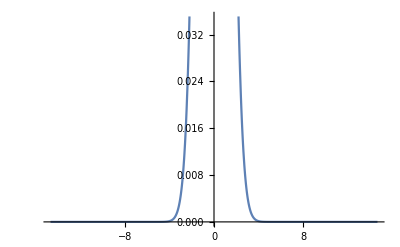

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

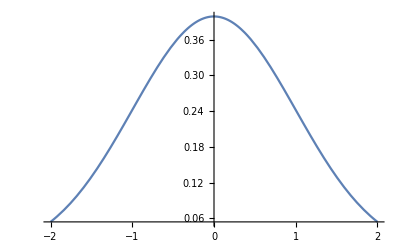

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-2,2},PlotRange->Full]
```

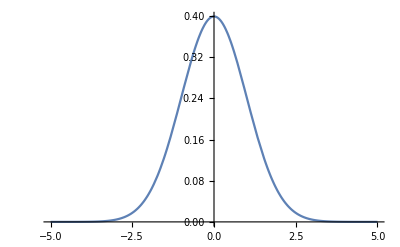

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-5,5},PlotRange->Full]
```

```mathematica
Length@data
```

5702

```mathematica
Plot[(ⅇ^(-(x-Length@5707)^2/2))/(√(2 π)),{x,-5,5},PlotRange->Full]
```

-Graphics-

General::munfl: Exp[-1.62849×10^7] is too small to represent as a normalized machine number; precision may be lost.

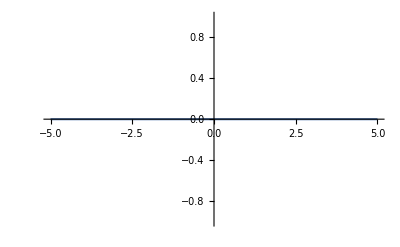

```mathematica
Plot[(ⅇ^(-(x-Length@data)^2/2))/(√(2 π)),{x,-5,5},PlotRange->Full]
```

```mathematica
Plot[(ⅇ^(-(x-5707)^2/2))/(√(2 π)),{x,-5,5}]
```

General::munfl: Exp[-1.63135×10^7] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
(ⅇ^(-(x-5707)^2/2))/(√(2 π))/.x->5700
```

1/(ⅇ^(49/2) √(2 π))

```mathematica
N[1/(ⅇ^(49/2) √(2 π))]
```

9.13472×10^-12

```mathematica
(ⅇ^(-(x-5707)^2/2))/(√(2 π))/.x->0
```

1/(ⅇ^(32569849/2) √(2 π))

```mathematica
N[1/(ⅇ^(32569849/2) √(2 π))]
```

General::munfl: Exp[-1.62849×10^7] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Table[
data[[i]] (ⅇ^(-(i-5707)^2/2))/(√(2 π)),{i,1,Length@data,1}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-6.80138×10^-317,1.34554×10^-300,2.42732×10^-284,5.13141×10^-269,4.55006×10^-254,-1.30637×10^-239,-1.86197×10^-225,-5.46456×10^-212,-7.7181×10^-199,-1.09638×10^-185,1.45515×10^-173,-2.38383×10^-162,-3.79575×10^-150,4.18517×10^-139,2.21927×10^-128,1.86099×10^-119,1.49076×10^-108,8.36809×10^-99,-2.04416×10^-90,7.5129×10^-82,-5.67189×10^-74,2.5484×10^-66,-2.1691×10^-59,2.45932×10^-51,6.04428×10^-47,-9.8007×10^-40,1.104×10^-35,5.75273×10^-29,-9.34051×10^-25,1.5302×10^-20,1.05671×10^-17,-7.13299×10^-14,2.91598×10^-11,-1.39909×10^-8}

```mathematica
Histogram[
data[[-100;;]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[
data[[-50;;]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Table[
{f,f[data]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,TrimmedMean,TrimmedVariance,N@Entropy@#&}}
]
```

{{Min,-0.247661},{Max,0.344714},{Max[#1]-Min[#1]&,0.592374},{Mean,0.00188709},{Quartiles,{-0.013156,0.000389994,0.015031}},{Variance,0.00139187},{Skewness,1.06925},{Kurtosis,13.5975},{TrimmedMean,0.000889221},{TrimmedVariance,0.000408161},{N[Entropy[#1]]&,8.62596}}

```mathematica
Grid@
Table[
{f,f[data]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,TrimmedMean,TrimmedVariance,N@Entropy@#&}}
]
```

Min | -0.247661
Max | 0.344714
Max[#1]-Min[#1]& | 0.592374
Mean | 0.00188709
Quartiles | {-0.013156,0.000389994,0.015031}
Variance | 0.00139187
Skewness | 1.06925
Kurtosis | 13.5975
TrimmedMean | 0.000889221
TrimmedVariance | 0.000408161
N[Entropy[#1]]& | 8.62596

```mathematica
Grid@
Table[
{f,f[Out[23]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,TrimmedMean,TrimmedVariance,N@Entropy@#&}}
]
```

Min | -1.39909×10^-8
Max | 2.91598×10^-11
Max[#1]-Min[#1]& | 1.40201×10^-8
Mean | -2.44858×10^-12
Quartiles | {0.,0.,0.}
Variance | 3.43295×10^-20
Skewness | -75.4912
Kurtosis | 5699.95
TrimmedMean | 0.
TrimmedVariance | 0.
N[Entropy[#1]]& | 0.0575149

```mathematica
Normalize@{1,2,3}
```

{1/(√14),√(2/7),3/(√14)}

```mathematica
N@{1/(√14),√(2/7),3/(√14)}
```

{0.267261,0.534522,0.801784}

```mathematica
Total@N@Range@5707
```

1.62878×10^7

```mathematica
Total@Normalize@Range@5707
```

2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290)

```mathematica
N[%32]
```

65.4265

```mathematica
Total@Range@3
```

6

```mathematica
Total@Normalize@Range@3
```

3 √(2/7)

```mathematica
N[3 √(2/7)]
```

1.60357

```mathematica
N@Normalize@Range@3
```

{0.267261,0.534522,0.801784}

```mathematica
(Normalize@{1,2,3})/(Total@Normalize@{1,2,3})
```

{1/6,1/3,1/2}

```mathematica
Total[{1/6,1/3,1/2}]
```

1

```mathematica
(Normalize@Range@5707)/(Total@Normalize@Range@5707)
```

{1/(√61974995290 (2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+5+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))),(√(2/30987497645))/(2992859 √(2/30987497645)+13+5984063/(√61974995290)),3/1,5701,1/1,(2853 √(2/30987497645))/(2992859 √(2/11)+14),(√(5707/10859470))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+11+√(5707/10859470)+5984063/(√61974995290))}
 |  |  |  |

```mathematica
Total[%40]
```

(2992859 √(2/30987497645))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(299673 √(5/12394999058))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(149998 √(10/6197499529))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(38281 √(13/4767307330))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(5786 √(130/476730733))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(31 √(439/141173110))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(11 √(761/81438890))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(16 √(878/70586555))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(6 √(1522/40719445))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(√(2195/28234622))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(3 √(2854/21715135))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(√(3805/16287778))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(√(4390/14117311))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(√(5707/10859470))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+5984063/(√61974995290 (2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(878/70586555)+6 √(1522/40719445)+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290)))

```mathematica
N[%41]
```

1.

```mathematica
Grid@
Table[
{f,f[Out[40]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,TrimmedMean,TrimmedVariance,N@Entropy@#&}}
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (√(2854/21715135))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(«1»)+6 √((«4»)/(«8»))+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(«1»)/5707.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (√(2854/21715135))/(2992859 √(2/30987497645)+299673 √(5/12394999058)+149998 √(10/6197499529)+38281 √(13/4767307330)+5786 √(130/476730733)+31 √(439/141173110)+11 √(761/81438890)+16 √(«1»)+6 √((«4»)/(«8»))+√(2195/28234622)+3 √(2854/21715135)+√(3805/16287778)+√(4390/14117311)+√(5707/10859470)+5984063/(√61974995290))+(«1»)/5137.

$Aborted[]

```mathematica
Grid@
Table[
{f,f[Out[40]]},
{f,{Min,Max,Max@#-Min@#&,Mean,Quartiles,Variance,Skewness,Kurtosis,TrimmedMean,TrimmedVariance,N@Entropy@#&}}
]
```